# Code for the manuscript: “Endocrine autoimmune disease as a fragility of immune-surveillance against hypersecreting mutants”

## Derivation of model equations

We start with the following model equations (see manuscript Methods). The equations describe a cell clone that proliferate at a rate that rises with the perceived signal u_i s, die at a natual turnover rate μ_0s_0, and is removed by ASHM at a rate that rises with antigen level u_i s,  relative to the average level of antigen in the tissue <u>s (Eq. 1). The normalization by average antigen level accounts for the effect of regulatory T-cells. The signal s is produced at rate p and removed at a rate that is enhanced by the secreted molecule y (Eq. 2). The molecule  is secreted by the different clones (Eq. 3):
{1. ds/dt== p-r y s,
2. dy/dt==b Sum[xi ui,i] s-α y,
3. dxi/dt== xi( μ_0(ui s-s_0)-a((ui s)/(<u>s))^n),
4. <u> == (∑xi ui)/(∑xi)}

Rescaling time μ_0 s_0 dt -> dt  and defining γ=a/μ_0 s_0, we get:

{4. ds/dt== p-r y s,
5. dy/dt==b Sum[xi ui,i] s-α y,
6. dxi/dt== xi( ui s/s0-1-γ(ui/(<u>))^n),
7. <u> == (∑xi ui)/(∑xi)}

We use a qusi-steady-state approximation for equations (4),(5):
8.  0 == p-r y s
9.  0 == b ∑x_i u_i s-α y

Solving (8),(9) for s gives s=(√p √α)/(√b √r √(∑x_i u_i))
Defining p̂=(p α)/(s_0^2 b r), we get that s/s_0=√((p̂)/(∑x_i u_i))
Plugging this into equation (6) we finally get the equation: 

  10. dxi/dt== xi( u_i √((p̂)/(∑x_i u_i))-1-γ(ui/(<u>))^n)
We use this equation to simulate model dynamics. We set p̂ to be (1+γ)^2  so that at steady-state x=1.  
From now on in this notebook, we replace p̂ notation to p, for convenience.

## Model Dynamics

```mathematica
(* Defining a numerical simulation of equation 10 with 3 competing populations: *)
```

```mathematica
solNF=ParametricNDSolveValue[
Flatten[{Table[{x[i]'[t]==x[i][t](u[i]Sqrt[p/Sum[x[i][t]u[i],{i,1,3}]]-1-γ (u[i]/U[t])^n),x[i][0]==x0[i]},{i,1,3}],U[t]==Sum[x[i][t]u[i],{i,1,3}]/Sum[x[i][t],{i,1,3}],U[0]==Sum[x0[i]u[i],{i,1,3}]/Sum[x0[i],{i,1,3}]}],
Flatten[{Table[x[i][t],{i,1,3}],U[t],Sqrt[p/Sum[x[i][t]u[i],{i,1,3}]],Sum[x[i][t]u[i],{i,1,3}]}],{t,0,10000},Flatten[{Table[x0[i],{i,1,3}],Table[u[i],{i,1,3}],γ,n,p}]]
```

ParametricFunction[<>]

```mathematica
(* Simulating dynamics with 3 populations: wild-type population with u1=1, hypo-sensing mutants with u2=0.5, and hyper-sensing mutants with u3=2. The 3 populations start from initial conditions x1=1 and x2,x3=0.5, representing a wild-type population with invading mutants: *)
```

```mathematica
With[{γ0= 0.25,p=(1+0.25)^2,smax={2,2,5},ymax={4,1.5,1.5},γ={0.01,0.25,2},tmax={12,12,3}},
Manipulate[
Table[{Plot[Evaluate[(solNF[x10,x20,x30,u1,u2,u3,γ[[ii]],n,p])[[;;3]]],{t,0,tmax[[ii]]},PlotRange->{All,{-0.1,ymax[[ii]]}},(*PlotLegends->{"x1 (under responsive)","x2 (normal)","x3 (over responsive)"},*)AxesLabel->{"time","#cells"}],
Plot[{Evaluate[(solNF[x10,x20,x30,u1,u2,u3,γ[[ii]],n,p])[[5]]/(1+γ0)],1},{t,0,tmax[[ii]]},PlotRange->{All,{0,smax[[ii]]}},AxesLabel->{"time","s/s^*"},PlotStyle->{Automatic,{Gray,Dashed,Thick}}]}
,{ii,{1,2,3}}],
{{x10,1},0.5,2},{{x20,0.5},0.5,2},{{x30,0.5},0.5,2},{{u1,1},0.5,10},{{u2,0.5},0.5,10},{{u3,2},0.5,10},{{n,1+1/γ0},Range[15]}]
]
```

## Phase portraits

```mathematica
(* Defining a numerical simulation of equation 10 with 2 competing populations: *)
```

```mathematica
solNF2=ParametricNDSolveValue[
Flatten[{Table[{x[i]'[t]==x[i][t](u[i]Sqrt[p/Sum[x[i][t]u[i],{i,1,2}]]-1-γ (u[i]/U[t])^h),x[i][0]==x0[i]},{i,1,2}],U[t]==Sum[x[i][t]u[i],{i,1,2}]/Sum[x[i][t],{i,1,2}],U[0]==Sum[x0[i]u[i],{i,1,2}]/Sum[x0[i],{i,1,2}]}],
Append[Table[x[i][t],{i,1,2}],U[t]],{t,0,10000},Flatten[{Table[x0[i],{i,1,2}],Table[u[i],{i,1,2}],γ,h,p}]]
```

ParametricFunction[<>]

```mathematica
(* Simulating dynamics with 2 populations: wild-type with u1=1 and hyper-sensing mutants with u2=2. We start from initial conditions x1=1 and x2=0.5 *)
```

```mathematica
With[{γ0= 0.25,p=(1+0.25)^2,cellmax={3.1,2.1,2.1},γ={0.01,0.25,2}},
Manipulate[
Table[
Show[
StreamPlot[{x1 (-1+u1 Sqrt[p/(x1 u1+x2 u2)]-((u1 (x1+x2))/(u1 x1+u2 x2))^n γ[[i]]),x2 (-1+u2 Sqrt[p/(x1 u1+x2 u2)]-((u2 (x1+x2))/(u1 x1+u2 x2))^n γ[[i]])},{x1,0.01,1.1},{x2,0.01,cellmax[[i]]},StreamPoints->Fine],
ParametricPlot[Evaluate@(solNF2[loc[[1]],loc[[2]],u1,u2,γ[[i]],n,p])[[;;2]],{t,0,tmax},PlotStyle->{Thick,Red}]
,ImageSize->300,FrameLabel-> {"normal cells","mutants"},PlotRange->{All,All}],
{i,{1,2,3}}],
{{u1,1},0.5,10},{{u2,2},0.5,10},{{n,1+1/γ0},{1,2,3,4,5,6,7,8,9,10,11,12,13,14}},{{loc,{1,0.5}}},{{tmax,100},1,1000}]
]
```

```mathematica
(* Arrows on the x axis could not be computed due to numerical simulations limitations.They were added to γ=0.25 phase portrait using analytical solution to this condition: *)
```

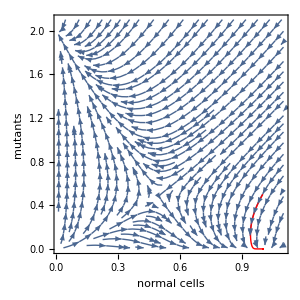
```mathematica
Show[-Graphics-,With[{γ= 0.25,u1=1,u2=2,h=5,p=1(1+0.25)^2},StreamPlot[{x1 (-1+1.25 √(1/x1)-0.25 ),0},{x1,0.01,1.1},{x2,0,0.001},StreamPoints->{Table[{i,0},{i,0.1,2,0.05}]}]],PlotRange->{{0,1.1},All} ]
```

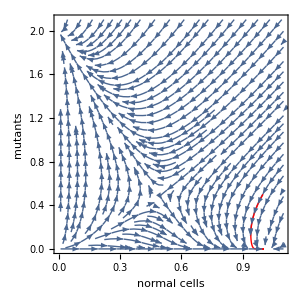

## Parameter scan

```mathematica
(* computation of parameter range regions: *)
```

We define two regimes: Autoimmunity, defined as a tissue loss of more than 50%; And mutation takeover range, defined as the range at which a mutant with u=2 takeover a population of wild-type cells with u=1.
Autoimmunity range calculation:
At steady-state, for wild-type with u=1, x_st=p/(1+γ_st)^2. We assume that at steady-state γ_st=1/(n-1), to establish an evolutionary stable strategy (see manuscript main text and Methods). 
We define autoimmunity parameters as such that give x_AID=1/2 x_st
This happens at n_AID=(1+γ_AID)/(1+√2+γ_AID):

```mathematica
FullSimplify@PowerExpand@FullSimplify@Solve[(p/(1+γ)^2)/(p/(1+1/(n-1))^2)== 1/2,n]
```

{{n→(1+γ)/(1+√2+γ)},{n→(1+γ)/(1-√2+γ)}}

Mutant takeover range calculation:
To find parameter range for which a mutant with u=2 takes over, we check the derivative at 3 directions next to the steady-state point (within a small distance α):

```mathematica
condition1[p_,u1_,u2_,γ_,n_]:=With[{x1=(p u1)/(1+γ)^2+α(p u1)/(1+γ)^2,x2=0},Chop[x1(u1 Sqrt[p/(x1 u1 + x2 u2)]-1-γ (u1/((x1 u1+x2 u2)/(x1+x2)))^n)]<0]
```

```mathematica
condition2[p_,u1_,u2_,γ_,n_]:=With[{x1=(p u1)/(1+γ)^2-α(p u1)/(1+γ)^2,x2=0}, Chop[x1(u1 Sqrt[p/(x1 u1 + x2 u2)]-1-γ (u1/((x1 u1+x2 u2)/(x1+x2)))^n)]>0]
```

```mathematica
condition3[p_,u1_,u2_,γ_,n_]:=With[{x1=(p u1)/(1+γ)^2,x2=α(p u2)/(1+γ)^2},Chop[x2(u2 Sqrt[p/(x1 u1 + x2 u2)]-1-γ (u2/((x1 u1+x2 u2)/(x1+x2)))^n)]<0]
```

```mathematica
mutationWinRegion2=With[{p=1,u1=1,u2=2},condition1[p,u1,u2,10^γ,n]&&condition2[p,u1,u2,10^γ,n]&&condition3[p,u1,u2,10^γ,n]];
```

```mathematica
FullSimplify[PowerExpand[mutationWinRegion2]]
```

√((1+α)/((1+10^γ)^2))<(1+α)/(1+10^γ)&&(1-α)/(1+10^γ)<√((1-α)/((1+10^γ)^2))&&(2 α (-1-2^(n+γ) 5^γ (1+2 α)^n (1+4 α)^-n+(2 Abs[1+10^γ])/(√(1+4 α))))/((1+10^γ)^2)<0

```mathematica
Quiet@Solve[-1-2^(n+γ) 5^γ (1+2 α)^n (1+4 α)^-n+(2 Abs[1+10^γ])/(√(1+4 α))==0,n]
```

{{n→(-γ Log[2]+Log[5^-γ (-1+(2 Abs[1+10^γ])/(√(1+4 α)))])/(Log[2]+Log[1+2 α]-Log[1+4 α])}}

```mathematica
(* Plotting parameter ranges: *)
```

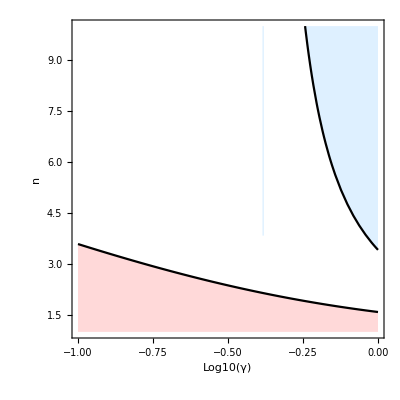

```mathematica
Show[
Plot[(-γ Log[2]+Log[5^-γ (-1+(2 Abs[1+10^γ])/(√(1+4 α)))])/(Log[2]+Log[1+2 α]-Log[1+4 α])/.α->10^-4,{γ,-1,0},PlotRange->{All,{1,10}},Filling->Bottom,FillingStyle->LightRed,PlotStyle->Black],
Plot[1+1/(-1+1/(√2)+10^γ/(√2)),{γ,-1,0},PlotRange->{All,{1,10}},RegionFunction->Function[{γ,h},h>0],Filling->Top,FillingStyle->LightBlue,PlotStyle->Black],
FrameLabel-> {"Log10(γ)","n"},AspectRatio->1,Axes->False,Frame->True]
```